Time elapsed: 0.318084

Fields at z = 100: 1.

Ax = 0.730719, Ay = 1.27949×10^-32, φ = 0.269281

φ[100] = 0.00762484

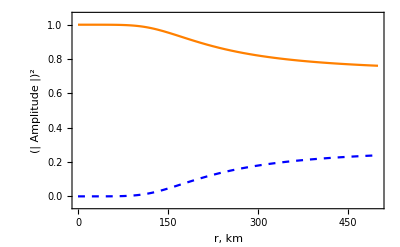

```mathematica
Clear["Global`*"]
time=AbsoluteTime[];

BSurf:=1.5*10^13;
R0:=12;

angleXi:=2.8Pi/6;
angleTheta:=Pi/6;
angleGamma:=Pi/4;

bR:=fDip*BSurf*(R0/(z+R0))^3*(Sin[angleXi]*Sin[angleTheta]*Cos[angleGamma]+Cos[angleXi]*Cos[angleTheta]);
bTheta:=gDip*0.5*BSurf*(R0/(z+R0))^3*(-Sin[angleXi]*Cos[angleTheta]*Cos[angleGamma]+Cos[angleXi]*Sin[angleTheta]);
bPhi:=gDip*0.5*BSurf*(R0/(z+R0))^3*(Sin[angleXi]*Sin[angleGamma]);

fDip:=-3/x^3(Log[1-x]+1/2 x(x+2));
gDip:=Sqrt[1-x](-2fDip+3/(1-x));
x:=4.134/(z+R0);

cosRotation:= bPhi/Sqrt[bPhi^2+bTheta^2]/.z->0;
sinRotation:=bTheta/Sqrt[bPhi^2+bTheta^2]/.z->0;

bRep:={bx->bTheta*sinRotation+bPhi*cosRotation,
	by->bTheta*cosRotation-bPhi*sinRotation,
	bz->bR};
	(*bPhi->BSurf*Cos[angleIteration]*(R0/(z+R0))^3};*)
(*0.5*BSurf*Sin[angleIteration]*(R0/(z+R0))^3*)

Bcrit:=4.4*10^13;
alpha:=1/137;



k0:=ω*5.06*10^9;
(*eV*5.06*10^9*)


B:={bx,by,bz};
Bunit:=B/Norm[B];

M:=((7 Bunit[[1]]^2 + 4 Bunit[[2]]^2)*μ[[1,1]] - 12 delta* Bunit[[1]]^2*Bunit[[2]]^2)/(μ[[1,1]]*μ[[2,2]]-16 delta^2 *Bunit[[1]]^2*Bunit[[2]]^2);
n:=((4 Bunit[[1]]^2 + 7 Bunit[[2]]^2)*μ[[2,2]] - 12 delta* Bunit[[1]]^2*Bunit[[2]]^2)/(μ[[1,1]]*μ[[2,2]]-16 delta^2 *Bunit[[1]]^2*Bunit[[2]]^2);
P:=(3μ[[1,1]]-4 delta (4 Bunit[[1]]^2 + 7 Bunit[[2]]^2))*Bunit[[1]]*Bunit[[2]]/
(μ[[1,1]]*μ[[2,2]]-16 delta^2 *Bunit[[1]]^2*Bunit[[2]]^2);

delta:=alpha/(45 Pi)*(Norm[B]^2/Bcrit^2);

Bmatrix:=Transpose[{B}].{B}/Norm[B]^2;
beta:=Norm[B]/Bcrit;

μ:=(1+a)*IdentityMatrix[3]+m *Bmatrix;
(*a:=-2 alpha/(45 Pi)*beta^2;
m:=-4 alpha/(45 Pi)*beta^2;*)

a:=-2 alpha/(9 Pi)*Log[1+beta^2*(1+0.25487*beta^(3/4))/(5*(1+0.75*beta^(5/4)))];
m=-alpha/(3Pi)*beta^2/(3.75+2.7*beta^(5/4)+beta^2);

(*Параметры АЛП*)
ω0=10;
g=6*10^(-20);
mass=3*10^(-8);

(*С красным смещением*)
ω:=ω0*Sqrt[(1-(4.134/R0))/(1-(4.134/(z+R0)))];

(*Без красного смещения*)
(*ω:=ω0;*)

(*Элементы матрицы М*)
deltaMx:=5.0*10^7*bx*g;
deltaMy:=5.0*10^7*by*g;

deltaMass:=2.5*10^9*mass^2*(1/ω);

deltaQEDxx:=k0 delta M/2;
deltaQEDyy:=k0 delta n/2;
deltaQEDxy:=k0 delta P/2;
deltaQEDyx:=deltaQEDxy;

(*Матрица М*)
mat:={{  deltaQEDxx,deltaQEDxy,deltaMx    },
	{deltaQEDyx,deltaQEDyy,deltaMy    },
	{deltaMx       ,deltaMy      ,-deltaMass}}/.bRep;

(*Матрица плотности ρ*)
rmat[z_]:={{r11[z],r12[z],r13[z]},{r21[z],r22[z],r23[z]},{r31[z],r32[z],r33[z]}};

oMode=True;

If[oMode,
(*O-mode*)
rmat0={{r11[0]==1,r12[0]==0,r13[0]==0},{r21[0]==0,r22[0]==0,r23[0]==0},{r31[0]==0,r32[0]==0,r33[0]==0}};
,
(*X-mode*)
rmat0={{r11[0]==0,r12[0]==0,r13[0]==0},{r21[0]==0,r22[0]==1,r23[0]==0},{r31[0]==0,r32[0]==0,r33[0]==0}};
];

upperLimitSolve:=1000;
upperLimitPlot:=500;

eqs=NDSolve[Join[{ⅈ rmat'[z]==rmat[z].mat-mat.rmat[z]/.bRep},rmat0],{r11[z],r22[z],r33[z]},{z,0,upperLimitSolve},MaxSteps->10^8, AccuracyGoal->5];
(*eqs=NDSolve[Join[{ⅈ rmat'[z]==rmat[z].mat-mat.rmat[z]/.bRep},rmat0],{r11[z],r22[z],r33[z]},{z,0,upperLimitSolve},MaxSteps->10^8, AccuracyGoal->5];*)

(*Print[mat/.bRep/.z->100//MatrixForm];*)
Print["Time elapsed: ",AbsoluteTime[]-time];
Print["Fields at z = 100: ",(bx/Sqrt[by^2+bx^2])/.bRep/.z->100];
Print["Ax = ",Re[r11[z]]/.eqs[[1]]/.z->upperLimitSolve,", Ay = ",Re[r22[z]]/.eqs[[1]]/.z->upperLimitSolve,", φ = ",Re[r33[z]]/.eqs[[1]]/.z->upperLimitSolve];
Print["φ[100] = ",Re[r33[z]]/.eqs[[1]]/.z->100];


p1=Plot[Re[Evaluate[{r11[z]}/.eqs]],{z,0,upperLimitPlot},PlotRange->{{0,upperLimitPlot},{-0.05,1.05}},PlotTheme->"Scientific",PlotStyle->Orange, PlotLegends->Placed[LineLegend[{Directive[Orange]},{Superscript["|A_x|",2]},LegendMarkerSize->30,LabelStyle->{FontSize->16,FontFamily->Times}],{0.92,0.8}], GridLines->None];
(*p2=Plot[Re[Evaluate[{r22[z]}/.eqs]],{z,0,upperLimitPlot},PlotRange->{{0,upperLimitPlot},{-0.1,1.05}},PlotTheme->"Scientific",PlotStyle->{Red,Dashed}, PlotLegends->Placed[LineLegend[{Directive[Red,Dashed]},{Superscript["|A_y|",2]},LegendMarkerSize->30,LabelStyle->{FontSize->14,FontFamily->Times}],{0.92,0.8}]];*)
p3=Plot[Re[Evaluate[{r33[z]}/.eqs]],{z,0,upperLimitPlot},PlotRange->{{0,upperLimitPlot},{-0.05,1.05}},PlotTheme->"Scientific",PlotStyle->{Blue,Dashed}, PlotLegends->Placed[LineLegend[{Directive[Blue,Dashed]},{Superscript["|φ|",2]},LegendMarkerSize->30,LabelStyle->{FontSize->16,FontFamily->Times}],{0.92,0.8}], GridLines->None];

(*Show[p1,p2,p3]*)
Show[p1,p3,FrameStyle->Directive[GrayLevel[0],14,AbsoluteThickness[1.0]],FrameLabel->{Style["r, km",16],Style[Superscript[" | Amplitude | " ,2],16]}]

zSet=Range[0,upperLimitPlot,upperLimitPlot/20];
bSet=Sqrt[bx^2+by^2]/.bRep/.z->zSet;

dataToFile = Transpose[{zSet,bSet}];

Export["C:\\Users\\Алексей\\Documents\\Axions_RXJ_Paper\\References_for_paper\\Mixing_data\\Radial_field_data.csv",dataToFile,"Table"];
```

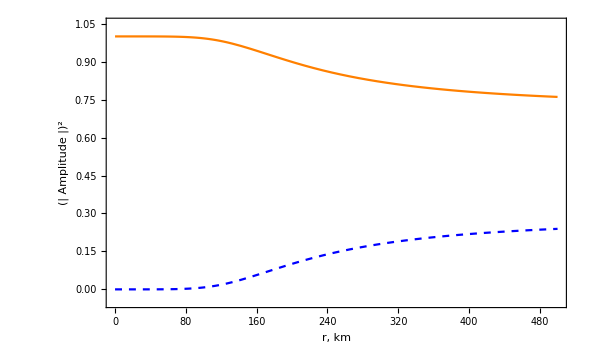

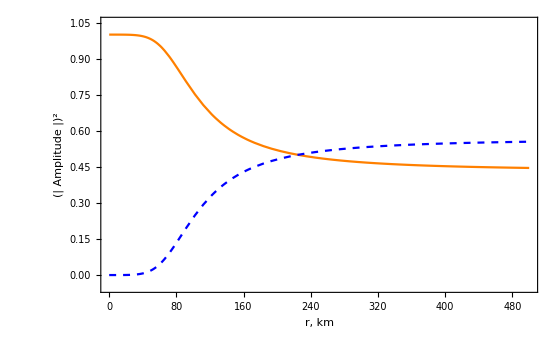

```mathematica
(*Проверка условий смешивания*)

For[dist:=1.,dist<10000,dist+=dist/3,
(*If[
((Abs[deltaQEDxx-deltaMass]<5Abs[deltaMx]||Abs[deltaQEDyy-deltaMass]<5Abs[deltaMy])&&(2Pi/Sqrt[(deltaQEDxx-deltaMass)^2+4deltaMx^2]<10dist||2Pi/Sqrt[(deltaQEDyy-deltaMass)^2+deltaMy^2]<dist))/.bRep/. z->dist,
Print[dist," < r < ",dist+dist],
Print[-1]
]*)

(*Print[dist," < r < ",dist+dist/3," : ",Abs[deltaQEDxx-deltaMass]<5Abs[deltaMx]||Abs[deltaQEDyy-deltaMass]<Abs[deltaMy]/.bRep/. z->dist]*)
Print[dist," < r < ",dist+dist/3," : ",2Pi/Sqrt[(deltaQEDxx-deltaMass)^2+4deltaMx^2]<5/3dist||2Pi/Sqrt[(deltaQEDyy-deltaMass)^2+4deltaMy^2]<dist/.bRep/. z->dist]
]
```

1. < r < 1.33333 : True

1.33333 < r < 1.77778 : True

1.77778 < r < 2.37037 : True

2.37037 < r < 3.16049 : True

3.16049 < r < 4.21399 : True

4.21399 < r < 5.61866 : True

5.61866 < r < 7.49154 : True

7.49154 < r < 9.98872 : True

9.98872 < r < 13.3183 : True

13.3183 < r < 17.7577 : True

17.7577 < r < 23.677 : True

23.677 < r < 31.5693 : True

31.5693 < r < 42.0924 : True

42.0924 < r < 56.1232 : True

56.1232 < r < 74.8309 : True

74.8309 < r < 99.7746 : True

99.7746 < r < 133.033 : False

133.033 < r < 177.377 : False

177.377 < r < 236.503 : False

236.503 < r < 315.337 : False

315.337 < r < 420.449 : False

420.449 < r < 560.599 : False

560.599 < r < 747.465 : False

747.465 < r < 996.62 : False

996.62 < r < 1328.83 : False

1328.83 < r < 1771.77 : False

1771.77 < r < 2362.36 : False

2362.36 < r < 3149.81 : False

3149.81 < r < 4199.75 : False

4199.75 < r < 5599.67 : False

5599.67 < r < 7466.22 : False

7466.22 < r < 9954.96 : False

9954.96 < r < 13273.3 : False

```mathematica
BSurf:=1.5*10^13;
R0:=12;
angleTheta:=Pi/3;
angleXi:=Pi/6;
angleGamma:=0;

bR:=BSurf*(R0/(z+R0))^3*(Sin[angleXi]*Sin[angleTheta]*Cos[angleGamma]+Cos[angleXi]*Cos[angleTheta]);
bTheta:=0.5*BSurf*(R0/(2z+R0))^3*(-Sin[angleXi]*Cos[angleTheta]*Cos[angleGamma]+Cos[angleXi]*Sin[angleTheta]);
bPhi:=-0.5*BSurf*(R0/(z+R0))^3*(Sin[angleXi]*Sin[angleGamma]);

cosRotation:= bPhi/Sqrt[bPhi^2+bTheta^2]/.z->0;
sinRotation:=bTheta/Sqrt[bPhi^2+bTheta^2]/.z->0;
Print["angleRotation: ",angleRotation];

bX:=bTheta*sinRotation+bPhi*cosRotation;
bY:=bTheta*cosRotation-bPhi*sinRotation;

Print["bTheta: ",bTheta/.z->0];
Print["bPhi: ",bPhi/.z->0];
Print["bX: ",bX/.z->0];
Print["bY: ",bY/.z->0];
```

angleRotation: angleRotation

bTheta: 3.75×10^12

bPhi: 0.

bX: 3.75×10^12

bY: 0.

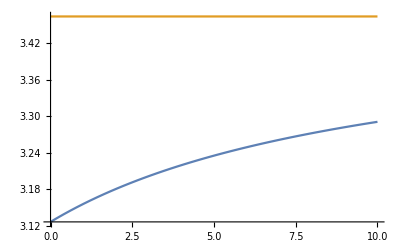

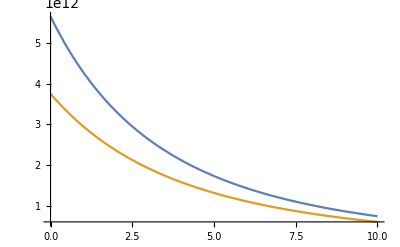

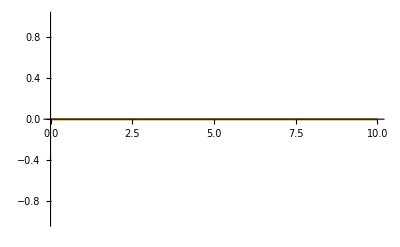

```mathematica
bR:=fDip*BSurf*(R0/(z+R0))^3*(Sin[angleXi]*Sin[angleTheta]*Cos[angleGamma]+Cos[angleXi]*Cos[angleTheta]);
bTheta:=gDip*0.5*BSurf*(R0/(z+R0))^3*(-Sin[angleXi]*Cos[angleTheta]*Cos[angleGamma]+Cos[angleXi]*Sin[angleTheta]);
bPhi:=gDip*0.5*BSurf*(R0/(z+R0))^3*(Sin[angleXi]*Sin[angleGamma]);

bRdip:=BSurf*(R0/(z+R0))^3*(Sin[angleXi]*Sin[angleTheta]*Cos[angleGamma]+Cos[angleXi]*Cos[angleTheta]);
bThetadip:=0.5*BSurf*(R0/(z+R0))^3*(-Sin[angleXi]*Cos[angleTheta]*Cos[angleGamma]+Cos[angleXi]*Sin[angleTheta]);
bPhidip:=0.5*BSurf*(R0/(z+R0))^3*(Sin[angleXi]*Sin[angleGamma]);

p4=Plot[{bR/bTheta,bRdip/bThetadip},{z,0,10}]
p5=Plot[{bTheta,bThetadip},{z,0,10}]
p5=Plot[{bPhi,bPhidip},{z,0,10}]
```

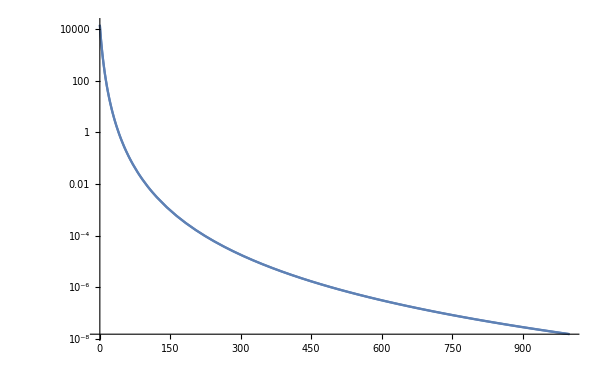

{8472.78,8387.14}

```mathematica
Clear["Global`*"]
time=AbsoluteTime[];

BSurf:=1.5*10^13;
R0:=12;

angleTheta:=Pi/6;
angleXi:=0Pi/6;
angleGamma:=0Pi/4;

bR:=fDip*BSurf*(R0/(z+R0))^3*(Sin[angleXi]*Sin[angleTheta]*Cos[angleGamma]+Cos[angleXi]*Cos[angleTheta]);
bTheta:=gDip*0.5*BSurf*(R0/(z+R0))^3*(-Sin[angleXi]*Cos[angleTheta]*Cos[angleGamma]+Cos[angleXi]*Sin[angleTheta]);
bPhi:=gDip*0.5*BSurf*(R0/(z+R0))^3*(Sin[angleXi]*Sin[angleGamma]);

fDip:=-3/x^3(Log[1-x]+1/2 x(x+2));
gDip:=Sqrt[1-x](-2fDip+3/(1-x));
x:=4.134/(z+R0);

cosRotation:= bPhi/Sqrt[bPhi^2+bTheta^2]/.z->0;
sinRotation:=bTheta/Sqrt[bPhi^2+bTheta^2]/.z->0;

bRep:={bx->bTheta*sinRotation+bPhi*cosRotation,
	by->bTheta*cosRotation-bPhi*sinRotation,
	bz->bR};
	(*bPhi->BSurf*Cos[angleIteration]*(R0/(z+R0))^3};*)
(*0.5*BSurf*Sin[angleIteration]*(R0/(z+R0))^3*)

Bcrit:=4.4*10^13;
alpha:=1/137;



k0:=ω*5.06*10^9;
(*eV*5.06*10^9*)


B:={bx,by,bz};
Bunit:=B/Norm[B];

M:=((7 Bunit[[1]]^2 + 4 Bunit[[2]]^2)*μ[[1,1]] - 12 delta* Bunit[[1]]^2*Bunit[[2]]^2)/(μ[[1,1]]*μ[[2,2]]-16 delta^2 *Bunit[[1]]^2*Bunit[[2]]^2);
n:=((4 Bunit[[1]]^2 + 7 Bunit[[2]]^2)*μ[[2,2]] - 12 delta* Bunit[[1]]^2*Bunit[[2]]^2)/(μ[[1,1]]*μ[[2,2]]-16 delta^2 *Bunit[[1]]^2*Bunit[[2]]^2);
P:=(3μ[[1,1]]-4 delta (4 Bunit[[1]]^2 + 7 Bunit[[2]]^2))*Bunit[[1]]*Bunit[[2]]/
(μ[[1,1]]*μ[[2,2]]-16 delta^2 *Bunit[[1]]^2*Bunit[[2]]^2);

delta:=alpha/(45 Pi)*(Norm[B]^2/Bcrit^2);

Bmatrix:=Transpose[{B}].{B}/Norm[B]^2;
beta:=Norm[B]/Bcrit;

μ:=(1+a)*IdentityMatrix[3]+m *Bmatrix;
(*a:=-2 alpha/(45 Pi)*beta^2;
m:=-4 alpha/(45 Pi)*beta^2;*)

a:=-2 alpha/(9 Pi)*Log[1+beta^2*(1+0.25487*beta^(3/4))/(5*(1+0.75*beta^(5/4)))];
m:=-alpha/(3Pi)*beta^2/(3.75+2.7*beta^(5/4)+beta^2);

(*Параметры АЛП*)
ω0=1;
g=6*10^(-20);
mass=10^(-6);

(*С красным смещением*)
ω:=ω0*Sqrt[(1-(4.134/R0))/(1-(4.134/(z+R0)))];

(*Без красного смещения*)
(*ω:=ω0;*)

(*Элементы матрицы М*)
deltaMx:=5.0*10^7*bx*g;
deltaMy:=5.0*10^7*by*g;

deltaMass:=2.5*10^9*mass^2*(1/ω);

deltaQEDxx:=k0 delta M/2;
deltaQEDyy:=k0 delta n/2;
deltaQEDxy:=k0 delta P/2;
deltaQEDyx:=deltaQEDxy;

(*Матрица М*)
mat:={{  deltaQEDxx,deltaQEDxy,deltaMx    },
	{deltaQEDyx,deltaQEDyy,deltaMy    },
	{deltaMx       ,deltaMy      ,deltaMass}}/.bRep;

(*Матрица плотности ρ*)
rmat[z_]:={{r11[z],r12[z],r13[z]},{r21[z],r22[z],r23[z]},{r31[z],r32[z],r33[z]}};

oMode=True;

If[oMode,
(*O-mode*)
rmat0={{r11[0]==1,r12[0]==0,r13[0]==0},{r21[0]==0,r22[0]==0,r23[0]==0},{r31[0]==0,r32[0]==0,r33[0]==0}};
,
(*X-mode*)
rmat0={{r11[0]==0,r12[0]==0,r13[0]==0},{r21[0]==0,r22[0]==1,r23[0]==0},{r31[0]==0,r32[0]==0,r33[0]==0}};
];

upperLimitSolve:=5000;
upperLimitPlot:=500;


altQED:=7k0*1.32*10^(-32)*bx^2;
deltaCEDTheta:=4.5*10^(-22)*ω*B.B;

LogPlot[{deltaQEDxx, altQED}/.bRep,{z,0,1000}]
{deltaQEDxx, altQED}/.bRep/.z->1
```